```mathematica
Clear[datalc];
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["PhysicalConstants`"];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\Prajwal\\Dropbox\\nEDM\\psi-nedm\\Analysis"]];
Print["(ASCII) Rawdata Directory: ",AscDir="C:\\Users\\Prajwal\\Dropbox\\nEDM\\rawdata"];
];
If[OS=="linux",
Print["Working Directory:",curDir=SetDirectory["/home/prajwal/Dropbox/nEDM/psi-nedm/Analysis"]];
Print["(faster) Rawdata Directory:",fastDir="/home/prajwal/nEDM/rawdata"];
Print["(ASCII) Rawdata Directory:",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];
];
Print["Runs in the list: ",runNum={11227}];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Real,Real,Real,Real};
runi=1;
datalc=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"-0_Leakage_current3.edm"],metaStructure2];
```

Working Directory: C:\Users\Prajwal\Dropbox\nEDM\psi-nedm\Analysis

(ASCII) Rawdata Directory: C:\Users\Prajwal\Dropbox\nEDM\rawdata

Runs in the list: {11227}

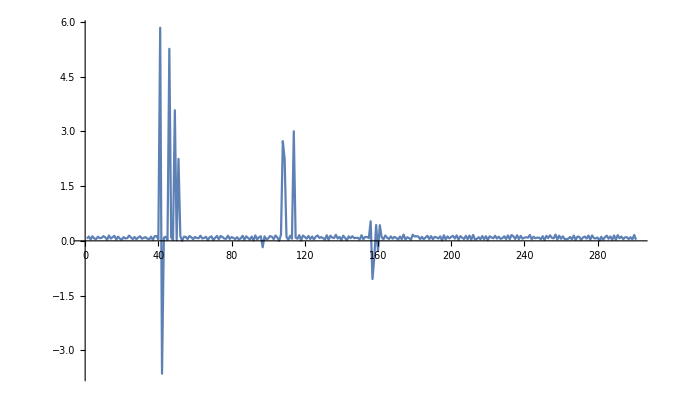

```mathematica
(*ListLinePlot[MovingAverage[datalc[[14*300;;16*300,4]],1][[;;;;1]],PlotRange->Full]*)
ListLinePlot[datalc[[71*300;;72*300,4]],PlotRange->Full]
```

```mathematica
Select[datalc[[;;,4]],(#>6)&]
MovingAverage[{1,2,3,4,5,6,7,8},2][[;;;;2]]
```

{6.679,6.944,6.148,7.554,6.669,6.643,6.306,6.537,7.017,6.525,6.234,6.577,6.555,6.535}

{3/2,7/2,11/2,15/2}

```mathematica
icycle=72;
data=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum[[runi]],10,6],"\\",IntegerString[runNum[[runi]],10,6],"_UCNdet_",IntegerString[icycle,10,3],"_0001.fast.ascii"],metaStructure];
Print["Size of event list in Cycle: ",dimdata=Dimensions[data][[1]]];
```

Size of event list in Cycle: 731

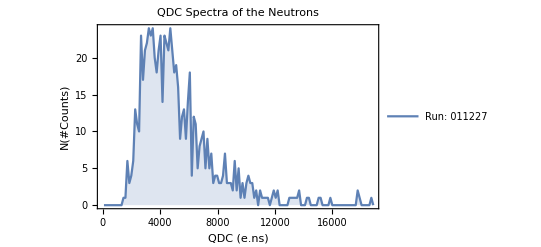

730

```mathematica
ChNum=4;binw=10;
(*histdata=HistogramList[Select[data[[1;;dimdata,{3,7}]],#[[1]]==ChNum&][[;;,2]],{100,3000,binw}];*)
histdata=HistogramList[data[[Round[1(*dimdata/1.022318*)];;dimdata,6]],{1,1400,binw}];
ptdat=Table[{0,0},{k,1,Dimensions[histdata[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata[[2]]][[1]],i++,
ptdat[[i]][[1]]=13.6*(histdata[[1]][[i]]+((-histdata[[1]][[1]]+histdata[[1]][[2]])/2));
ptdat[[i]][[2]]=histdata[[2]][[i]];
];
ListLinePlot[{ptdat},PlotRange->Full,Frame->True,PlotRange->Full,FrameLabel->{"QDC (e.ns)","N(#Counts)"},TicksStyle->Directive[FontSize->40],LabelStyle->{18},PlotLegends->{"Run: 011227"},Filling->Axis,ImageSize->{1000},PlotLabel->"QDC Spectra of the Neutrons"]
Total[histdata[[2]]]
```

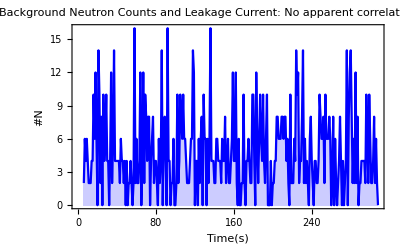
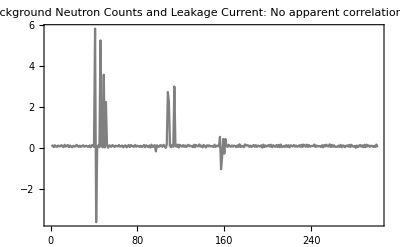

729

```mathematica
histdata2=HistogramList[data[[1;;dimdata,4]]/1000000000,{1,304,1}];
ptdat=Table[{0,0},{k,1,Dimensions[histdata2[[2]]][[1]]}];
For[i=1,i<=Dimensions[histdata2[[2]]][[1]],i++,
ptdat[[i]][[1]]=(histdata2[[1]][[i]]+((-histdata[[1]][[1]]+histdata[[1]][[2]])/2));
ptdat[[i]][[2]]=2*histdata2[[2]][[i]];
];
Overlay[{ListLinePlot[ptdat,PlotRange->Full,ImagePadding->100,PlotRange->Full,TicksStyle->Directive[FontSize->40],FrameLabel->{"Time(s)","#N"},LabelStyle->{18},Filling->Axis,ImageSize->{1000},PlotStyle->Blue,Frame->{True,True,True,False},FrameStyle->{Automatic,Blue,Automatic,Automatic},PlotLabel->"Background Neutron Counts and Leakage Current: No apparent correlation found!"],
ListLinePlot[datalc[[71*300;;72*300,4]],ImagePadding->100,PlotRange->Full,TicksStyle->Directive[FontSize->40],LabelStyle->{18},Filling->Axis,ImageSize->{1000},PlotStyle->Gray,Frame->{False,False,False,True},FrameTicks->All,FrameStyle->{Automatic,Automatic,Automatic,Gray},FrameLabel->{"","","",Rotate["Leakage Current (nA)",180Degree]},PlotLabel->"Background Neutron Counts and Leakage Current: No apparent correlation found!"]}]
Total[histdata2[[2]]]
```